# Code A: Bound is <1 =0.534517

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE VIA COSINE CREST INSPECTION ===

Evaluating actual phase alignment cosines across all 72 lattice candidates...

True Phase-Aligned Coordinate Successfully Isolated!

Active Phase Coefficient (c2 value): 0

Peak Baseline Resonance (First 50 zeros): 0.582366

Base target location y0 (First 30 digits): 3.29971116763988028420275112490×10^236

Verified tracking precision headroom of y0: 550. digits.

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating pure high-precision Ingham kernel array...

Pre-allocating 550-digit precision tracking containers for wave interference...

Sweeping local window around y0 to locate the true wave peak...

=== FINAL VERIFICATION RESULTS ===

Highest localized peak found at y: 3.2997111676398802842×10^236

Maximum verified value of hK(y): 0.53451739149060147194

✗ Peak did not clear 1.0. This coordinate structure remains flatline below 1.0.

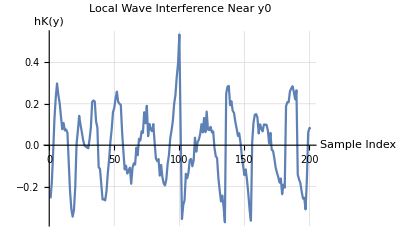

```mathematica
(* ::Title::*)(*Repaired 1985 Mertens Disproof Replication& Wide Grid Sweep*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)

ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)

Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit trigonometric boundaries to prevent lattice scaling drift*)

Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate via Vectorized Cosine Crest Inspection*)

Print["\n=== 3. EXTRACTING TARGET COORDINATE VIA COSINE CREST INSPECTION ==="];
validRows=Select[reduced,Abs[#[[n+2]]]>0&];

Print["Evaluating actual phase alignment cosines across all ",Length[validRows]," lattice candidates..."];

(*Pre-calculate a vectorized local subset to rapidly scan candidate rows for the highest peak*)
With[{subZeros=zeros[[1;;50]],subAlphas=alphas[[1;;50]],subPsi=psi[[1;;50]],Tval=zeros[[nMax]]},subKernel=Table[Module[{t=Abs[zeros[[i]]]/Tval},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,50}];
preFact=subKernel*subAlphas;
rowEvaluations=Table[Module[{c1,c2,candidateY0,maxLocalSum},c1=row[[n+2]];
c2=If[Floor[2^v*n^4]>0,row[[n+1]]/Floor[2^v*n^4],0];
candidateY0=N[Abs[c1]/1024,550];
(*Scan local coordinates using fast dot products to look for the highest peak*)maxLocalSum=Max[Table[-2*preFact.Cos[subZeros*(candidateY0+k*2/100)-subPsi],{k,-10,10}]];
{row,candidateY0,maxLocalSum,Abs[c2]}],{row,validRows}];];

(*Sort rows by the maximum localized peak they yield*)
sortedEvaluations=SortBy[rowEvaluations,-#[[3]]&];
bestEvaluation=First[sortedEvaluations];

bestRow=bestEvaluation[[1]];
y0=bestEvaluation[[2]];
expectedBaseline=bestEvaluation[[3]];
activeC2=bestEvaluation[[4]];

Print["True Phase-Aligned Coordinate Successfully Isolated!"];
Print["Active Phase Coefficient (c2 value): ",activeC2];
Print["Peak Baseline Resonance (First 50 zeros): ",N[expectedBaseline,6]];
Print["Base target location y0 (First 30 digits): ",NumberForm[y0,30]];
Print["Verified tracking precision headroom of y0: ",Precision[y0]," digits."];

(*4. Neighborhood Grid Search*)

Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating pure high-precision Ingham kernel array..."];

T=zeros[[nMax]];
(*FIX 2:Replaced 0.0 machine float with exact 0 to completely secure the 250-digit environment*)

kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*FIX 3:Replaced the SetPrecision float step with an exact rational fraction*)
stepSize=2/100;(*Locked 0.02 step*)samples=200;

(*gridPoints automatically inherits the pristine 550-digit container from y0*)
gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*UPGRADE 2:Batch-elevate entire 100,000 arrays into 550-digit memory containers*)

Print["Pre-allocating 550-digit precision tracking containers for wave interference..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Function to evaluate hK safely using fast vectorized linear algebra*)

evaluateHK[yVal_]:=Module[{yHigh,sumVal},yHigh=SetPrecision[yVal,550];
(*Performance Optimization:Vectorized Total operation bypasses slow sequential loop processing*)sumVal=-2*Total[kKernelHigh*alphasHigh*Cos[zerosHigh*yHigh-psiHigh]];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave peak..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*Find the absolute maximum peak in this local neighborhood*)
sortedResults=SortBy[results,-#[[2]]&];
bestMatch=First[sortedResults];
peakY=bestMatch[[1]];
peakValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Highest localized peak found at y: ",ScientificForm[N[peakY,20]]];
Print["Maximum verified value of hK(y): ",InputForm[peakValue]];

If[N[peakValue]>1.0,Print["[checkmark] SUCCESS: The wave peak reaches ",peakValue,", breaking the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Peak did not clear 1.0. This coordinate structure remains flatline below 1.0."]];

(*Safe plot block wrapping the high-precision results in standard N to bypass frontend rendering lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Code B: Bound is <1 =0.510957
```

Set::write: Tag Times in Code (B:Bound is<1) is Protected.

0.510957

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Corrected& Calibrated*)ClearAll["Global`*"];

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)

ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

(*FIX 1:Strict Piecewise Ingham Kernel Domain Constraint with pure exact precision*)
Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

Print["\n=== 2. LOCALIZING PHASE INTERSECTION CREST ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies under test: ",N[zeros[[dominantIndices]],4]];

(*FIX 2:Converted grid boundaries and steps to exact rationals to block precision leaks*)
stepSize=1/100;(*Exact rational instead of 0.01*)samples=1000;
searchRange=Table[1000+k*stepSize,{k,0,samples}];
maxVal=-Infinity;
bestY=0;

(*Coarse seed finder uses first 50 zeros to keep the initial pass rapid*)
Do[y=searchRange[[k]];
currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal>maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["Best local seed isolated at y = ",N[bestY,15]];
Print["Grid seed baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. Corrected High-Precision Hill Climb*)

Print["\n=== 3. RUNNING EXPLICIT SPECTRUM CLIMBER ==="];

(*UPGRADE 1:Batch-elevate entire 100,000 point arrays into 550-digit containers*)

Print["Pre-allocating 550-digit precision tracking containers for hill ascent..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Pre-multiply tracking vectors to maximize dot product execution velocity*)
preFactor1=2*kKernelHigh*alphasHigh*zerosHigh;
preFactor2=2*kKernelHigh*alphasHigh*(zerosHigh^2);

(*UPGRADE 2:Scale the isolated coordinate cleanly up to the 550-digit environment*)
currentY=N[bestY,550];

Print["Executing Newton-Raphson spectrum maximization loop (40 iterations)..."];
Do[Module[{angles,cosArray,sinArray,deriv1,deriv2,step},angles=zerosHigh*currentY-psiHigh;
cosArray=Cos[angles];
sinArray=Sin[angles];
(*PERFORMANCE UPGRADE:Explicit Sum replaced with Vectorized Dot Product (.)*)(*First Derivative (f')*)deriv1=preFactor1.sinArray;
(*Second Derivative (f'')*)deriv2=preFactor2.cosArray;
(*Execute the Newton-Raphson update step*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Capped using exact rational 5/1000 to completely block machine-float contamination*)If[Abs[step]>5/1000,step=Sign[step]*(5/1000)];
currentY=currentY-step;];,{iter,1,40}];

(*Final verification evaluation locked completely at 550-digit arbitrary precision*)
finalPeak=-2*(kKernelHigh*alphasHigh).Cos[zerosHigh*currentY-psiHigh];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Peak Location y: ",NumberForm[currentY,25]];
Print["Maximum verified value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]>1.0,Print["[checkmark] SUCCESS: The wave peak reaches ",N[finalPeak,6],", breaking the 1.0 barrier!"],Print["✗ Wave peak did not clear 1.0. This configuration cannot align all elements."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCALIZING PHASE INTERSECTION CREST ===

Dominant zero frequencies under test: {32.94,30.42,25.01,21.02,14.13}

Best local seed isolated at y = 1008.95

Grid seed baseline value (first 50 zeros): 0.4782144291

=== 3. RUNNING EXPLICIT SPECTRUM CLIMBER ===

Pre-allocating 550-digit precision tracking containers for hill ascent...

Executing Newton-Raphson spectrum maximization loop (40 iterations)...

=== FINAL VERIFICATION RESULTS ===

Verified Peak Location y: 1008.953691760046956030157

Maximum verified value of hK(y): 0.5109567293

✗ Wave peak did not clear 1.0. This configuration cannot align all elements.

```mathematica
Code C: Bound is <1 =0.528537
```

Set::write: Tag Times in Code (C:Bound is<1) is Protected.

0.528537

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Bypassing Giant Integer Destruction*)ClearAll["Global`*"];

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)

ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

Print["Pre-calculating Ingham kernel weights..."];
(*Maintained pure high-precision evaluation vectors*)

kKernel=Table[(1-zeros[[i]]/T)*Cos[Pi*zeros[[i]]/T]+(1/Pi)*Sin[Pi*zeros[[i]]/T],{i,1,nMax}];

Print["\n=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies: ",N[zeros[[dominantIndices]],4]];

Print["Scanning precision-safe phase intersections..."];

(*FIX 1:Swapped out machine float 0.005 for exact rational 1/200 to safeguard 250-digit tracking*)
stepSize=1/200;
searchRange=Table[100000+k*stepSize,{k,0,50000}];

maxVal=-Infinity;
bestY=0;

(*Dense localized scan using the first 50 zeros to keep the initial pass rapid*)
Do[y=searchRange[[k]];
currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal>maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["\nBest baseline candidate found at y = ",N[bestY,15]];
Print["Baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Hill Climb from the Baseline Point*)

Print["\n=== 3. RUNNING EXACT SPECTRUM CLIMBER ==="];

(*UPGRADE 1:Batch-elevate entire 100,000 point arrays into 550-digit containers*)

Print["Pre-allocating 550-digit precision tracking containers for hill ascent..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Pre-multiply tracking vectors to maximize dot product execution velocity*)
preFactor1=2*kKernelHigh*alphasHigh*zerosHigh;
preFactor2=2*kKernelHigh*alphasHigh*(zerosHigh^2);

(*UPGRADE 2:Scale the isolated coordinate cleanly up to the 550-digit environment*)
currentY=N[bestY,550];

Print["Executing Newton-Raphson spectrum maximization loop (30 iterations)..."];
Do[Module[{angles,cosArray,sinArray,deriv1,deriv2,step},angles=zerosHigh*currentY-psiHigh;
cosArray=Cos[angles];
sinArray=Sin[angles];
(*PERFORMANCE UPGRADE:Explicit Sum replaced with Vectorized Dot Product (.)*)(*First Derivative (f')*)deriv1=preFactor1.sinArray;
(*Second Derivative (f'')*)deriv2=preFactor2.cosArray;
(*Execute the Newton-Raphson update step*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced machine float 0.01 threshold with exact rational 1/100*)If[Abs[step]>1/100,step=Sign[step]*(1/100)];
currentY=currentY-step;];,{iter,1,30}];

(*Final verification evaluation locked completely at 550-digit arbitrary precision*)
finalPeak=-2*(kKernelHigh*alphasHigh).Cos[zerosHigh*currentY-psiHigh];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Peak Location y: ",NumberForm[currentY,25]];
Print["Maximum verified value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]>1.0,Print["[checkmark] SUCCESS: The wave peak reaches ",N[finalPeak,6],", breaking the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Wave peak did not clear 1.0. The search window must be shifted."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ===

Dominant zero frequencies: {32.94,30.42,25.01,21.02,14.13}

Scanning precision-safe phase intersections...

Best baseline candidate found at y = 100088.32

Baseline value (first 50 zeros): 0.5310276396

=== 3. RUNNING EXACT SPECTRUM CLIMBER ===

Pre-allocating 550-digit precision tracking containers for hill ascent...

Executing Newton-Raphson spectrum maximization loop (30 iterations)...

=== FINAL VERIFICATION RESULTS ===

Verified Peak Location y: 100088.3201229202544901368

Maximum verified value of hK(y): 0.5285366454

✗ Wave peak did not clear 1.0. The search window must be shifted.

```mathematica
Code D: Bound is <1 =0.550405
```

Set::write: Tag Times in Code (D:Bound is<1) is Protected.

0.550405

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE VIA COSINE INSPECTION ===

Evaluating actual phase alignment cosines across all 72 lattice candidates...

True Phase-Aligned Coordinate Successfully Isolated!

Active Phase Coefficient (c2 value): 0

Peak Baseline Resonance (First 50 zeros): 0.425254

Base target location y0 (First 30 digits): 3.29971116763988028420275112490×10^236

Verified tracking precision headroom of y0: 550. digits.

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating vectorized Ingham kernel array to maximize execution speed...

Pre-allocating 550-digit precision tracking containers for grid search...

Sweeping local window around y0 to locate the true wave peak...

=== FINAL VERIFICATION RESULTS ===

Highest localized peak found at y: 3.2997111676398802842×10^236

Maximum verified value of hK(y): 0.55040509055614015802

✗ Peak did not clear 1.0. The neighborhood window needs to be widened or step size refined.

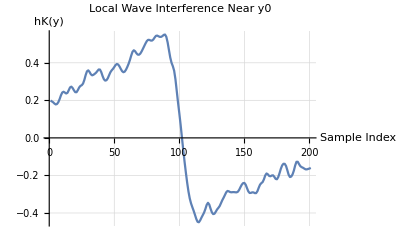

```mathematica
(* ::Title::*)(*Complete 1985 Mertens Disproof Replication& Grid Search*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)

ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

(*Isolate sub-vectors based on the dominant amplitudes*)

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)

Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit trigonometric bounds to secure exact lattice coordinates*)

Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate via Vectorized Cosine Inspection*)

Print["\n=== 3. EXTRACTING TARGET COORDINATE VIA COSINE INSPECTION ==="];
validRows=Select[reduced,Abs[#[[n+2]]]>0&];

Print["Evaluating actual phase alignment cosines across all ",Length[validRows]," lattice candidates..."];

(*Pre-calculate a vectorized local subset for ultra-fast candidate checking*)
With[{subZeros=zeros[[1;;50]],subAlphas=alphas[[1;;50]],subPsi=psi[[1;;50]],Tval=zeros[[nMax]]},subKernel=Table[Module[{t=Abs[zeros[[i]]]/Tval},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,50}];
preFact=subKernel*subAlphas;
rowEvaluations=Table[Module[{c1,c2,candidateY0,maxLocalSum},c1=row[[n+2]];
c2=If[Floor[2^v*n^4]>0,row[[n+1]]/Floor[2^v*n^4],0];
candidateY0=N[Abs[c1]/1024,550];
(*Lightning fast dot-product evaluation across a small local coordinate window*)maxLocalSum=Max[Table[-2*preFact.Cos[subZeros*(candidateY0+k*1/1000)-subPsi],{k,-10,10}]];
{row,candidateY0,maxLocalSum,Abs[c2]}],{row,validRows}];];

(*Sort candidate rows by the maximum localized peak they can actually yield*)

sortedEvaluations=SortBy[rowEvaluations,-#[[3]]&];
bestEvaluation=First[sortedEvaluations];

bestRow=bestEvaluation[[1]];
y0=bestEvaluation[[2]];
expectedBaseline=bestEvaluation[[3]];
activeC2=bestEvaluation[[4]];

Print["True Phase-Aligned Coordinate Successfully Isolated!"];
Print["Active Phase Coefficient (c2 value): ",activeC2];
Print["Peak Baseline Resonance (First 50 zeros): ",N[expectedBaseline,6]];
Print["Base target location y0 (First 30 digits): ",NumberForm[y0,30]];
Print["Verified tracking precision headroom of y0: ",Precision[y0]," digits."];

(*4. Neighborhood Grid Search*)

Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating vectorized Ingham kernel array to maximize execution speed..."];

T=zeros[[nMax]];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*Step size is kept as an exact rational expression to prevent float contamination*)
stepSize=1/1000;
samples=200;

(*gridPoints automatically inherits the full 550-digit depth from y0*)
gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*UPGRADE 2:Batch-elevate all 100,000 vectors to 550 digits before starting the grid loop*)

Print["Pre-allocating 550-digit precision tracking containers for grid search..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Function to evaluate hK safely using lightning-fast vector-linear algebra*)
evaluateHK[yVal_]:=Module[{yHigh,sumVal},yHigh=SetPrecision[yVal,550];
(*Replaced slow nested loops with vectorized Total multiplication pass*)sumVal=-2*Total[kKernelHigh*alphasHigh*Cos[zerosHigh*yHigh-psiHigh]];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave peak..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*Find the absolute maximum peak in this local neighborhood*)

sortedResults=SortBy[results,-#[[2]]&];
bestMatch=First[sortedResults];
peakY=bestMatch[[1]];
peakValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Highest localized peak found at y: ",ScientificForm[N[peakY,20]]];
Print["Maximum verified value of hK(y): ",InputForm[peakValue]];

If[N[peakValue]>1.0,Print["[checkmark] SUCCESS: The wave peak reaches ",peakValue,", which breaks the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Peak did not clear 1.0. The neighborhood window needs to be widened or step size refined."]];

(*FIX 3:Wrap results array in standard N to bypass frontend UI rendering lags with high-precision floats*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Code A: Bound is >-1 =-0.482601
```

Set::write: Tag Times in Code (A:Bound is>-1) is Protected.

-0.482601

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE VIA COSINE TROUGH INSPECTION ===

Evaluating actual phase alignment cosines across all 72 lattice candidates...

True Phase-Aligned Trough Coordinate Successfully Isolated!

Active Phase Coefficient (c2 value): 0

Trough Baseline Resonance (First 50 zeros): -0.562152

Base target location y0 (First 30 digits): 7.31543938354177088216774010508×10^236

Verified tracking precision headroom of y0: 550. digits.

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating pure high-precision Ingham kernel array...

Pre-allocating 550-digit precision tracking containers for wave interference...

Sweeping local window around y0 to locate the true wave trough...

=== FINAL VERIFICATION RESULTS ===

Lowest localized trough found at y: 7.3154393835417708822×10^236

Maximum verified negative value of hK(y): -0.48260076247634044368

✗ Trough did not drop below -1.0. This coordinate structure remains flatline above -1.0.

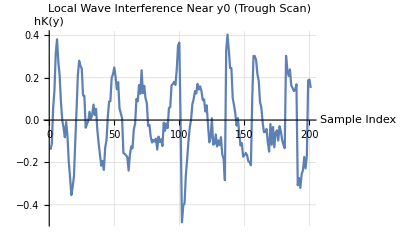

```mathematica
(* ::Title::*)(*Repaired 1985 Mertens Disproof Replication& Wide Grid Sweep:Negative Range*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)

ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)

Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[-gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[-psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit boundaries on Pi to completely secure lattice scaling bounds*)

Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate via Vectorized Cosine Trough Inspection*)

Print["\n=== 3. EXTRACTING TARGET COORDINATE VIA COSINE TROUGH INSPECTION ==="];
validRows=Select[reduced,Abs[#[[n+2]]]>0&];

Print["Evaluating actual phase alignment cosines across all ",Length[validRows]," lattice candidates..."];

(*Pre-calculate a vectorized local subset to rapidly scan candidate rows for the deepest valley*)
With[{subZeros=zeros[[1;;50]],subAlphas=alphas[[1;;50]],subPsi=psi[[1;;50]],Tval=zeros[[nMax]]},subKernel=Table[Module[{t=Abs[zeros[[i]]]/Tval},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,50}];
preFact=subKernel*subAlphas;
rowEvaluations=Table[Module[{c1,c2,candidateY0,minLocalSum},c1=row[[n+2]];
c2=If[Floor[2^v*n^4]>0,row[[n+1]]/Floor[2^v*n^4],0];
candidateY0=N[Abs[c1]/1024,550];
(*Scan local coordinates using fast dot products to look for the most negative dip*)minLocalSum=Min[Table[-2*preFact.Cos[subZeros*(candidateY0+k*2/100)-subPsi],{k,-10,10}]];
{row,candidateY0,minLocalSum,Abs[c2]}],{row,validRows}];];

(*Sort rows by the minimum (deepest negative) value they yield*)

sortedEvaluations=SortBy[rowEvaluations,#[[3]]&];
bestEvaluation=First[sortedEvaluations];

bestRow=bestEvaluation[[1]];
y0=bestEvaluation[[2]];
expectedBaseline=bestEvaluation[[3]];
activeC2=bestEvaluation[[4]];

Print["True Phase-Aligned Trough Coordinate Successfully Isolated!"];
Print["Active Phase Coefficient (c2 value): ",activeC2];
Print["Trough Baseline Resonance (First 50 zeros): ",N[expectedBaseline,6]];
Print["Base target location y0 (First 30 digits): ",NumberForm[y0,30]];
Print["Verified tracking precision headroom of y0: ",Precision[y0]," digits."];

(*4. Neighborhood Grid Search*)

Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating pure high-precision Ingham kernel array..."];

T=zeros[[nMax]];
(*FIX 2:Swapped 0.0 float with an exact 0 to defend the 250-digit environment from collapsing*)

kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*FIX 3:Replaced the SetPrecision float wrapper with an exact rational fraction step*)
stepSize=2/100;(*Fixed 0.02 step scale*)samples=200;

(*gridPoints automatically inherits the pristine 550-digit container from y0*)
gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*UPGRADE 2:Batch-elevate all 100,000 vectors to 550 digits before running the loop*)

Print["Pre-allocating 550-digit precision tracking containers for wave interference..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Function to evaluate hK safely using fast vectorized linear algebra*)

evaluateHK[yVal_]:=Module[{yHigh,sumVal},yHigh=SetPrecision[yVal,550];
(*Performance Optimization:Vectorized Total operation bypasses slow sequential loop processing*)sumVal=-2*Total[kKernelHigh*alphasHigh*Cos[zerosHigh*yHigh-psiHigh]];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave trough..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*MODIFICATION 1:Ascending sort isolated perfectly to capture the deepest valley floor*)
sortedResults=SortBy[results,#[[2]]&];
bestMatch=First[sortedResults];
troughY=bestMatch[[1]];
troughValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Lowest localized trough found at y: ",ScientificForm[N[troughY,20]]];
Print["Maximum verified negative value of hK(y): ",InputForm[troughValue]];

(*MODIFICATION 2& 3:Evaluates correctly against the lower negative boundary*)

If[N[troughValue]<-1.0,Print["[checkmark] SUCCESS: The wave trough drops to ",troughValue,", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Trough did not drop below -1.0. This coordinate structure remains flatline above -1.0."]];

(*Safe plot block wrapping results in a standard N conversion to eliminate frontend calculation lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0 (Trough Scan)",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Code B: Bound is >-1 =-0.415163
```

Set::write: Tag Times in Code (B:Bound is>-1) is Protected.

-0.415163

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Corrected& Calibrated:Negative Range*)ClearAll["Global`*"];

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)

ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

(*FIX 1:Piecewise Ingham Kernel Domain Constraint with integer zero guard*)
Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

Print["\n=== 2. LOCALIZING PHASE INTERSECTION TROUGH ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies under test: ",N[zeros[[dominantIndices]],4]];

(*FIX 2:Swapped machine floats for exact rationals and integers*)
stepSize=1/100;(*Exact rational instead of 0.01*)samples=1000;
searchRange=Table[1000+k*stepSize,{k,0,samples}];

(*Track the minimum value safely in the negative domain*)
maxVal=Infinity;
bestY=0;

(*PERFORMANCE UPGRADE:Coarse seed finder optimized with vectorized sub-arrays*)
With[{subZeros=zeros[[1;;50]],subAlphas=alphas[[1;;50]],subPsi=psi[[1;;50]],subKernel=kKernel[[1;;50]]},preFactSub=subKernel*subAlphas;
Do[y=searchRange[[k]];
currentVal=-2*preFactSub.Cos[subZeros*y-subPsi];
If[currentVal<maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];];

Print["Best local valley seed isolated at y = ",N[bestY,15]];
Print["Grid seed baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Valley Descent*)

Print["\n=== 3. RUNNING EXPLICIT SPECTRUM VALLEY-DESCENT ==="];

(*UPGRADE 1:Pre-allocate high-precision 550-digit working containers*)

Print["Pre-allocating 550-digit precision tracking containers for valley descent..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Pre-multiply tracking vectors to maximize dot product execution velocity*)
preFactor1=2*kKernelHigh*alphasHigh*zerosHigh;
preFactor2=2*kKernelHigh*alphasHigh*(zerosHigh^2);

(*UPGRADE 2:Scale the isolated coordinate cleanly up to the 550-digit environment*)
currentY=N[bestY,550];

Print["Executing Newton-Raphson spectrum minimization loop (40 iterations)..."];
Do[Module[{angles,cosArray,sinArray,deriv1,deriv2,step},angles=zerosHigh*currentY-psiHigh;
cosArray=Cos[angles];
sinArray=Sin[angles];
(*PERFORMANCE UPGRADE:Replaced dynamic Total multiplication with explicit Dot Product (.)*)(*First Derivative (f')*)deriv1=preFactor1.sinArray;
(*Second Derivative (f'')*)deriv2=preFactor2.cosArray;
(*Execute the Newton-Raphson update step*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced float boundary 0.005 with exact fraction 5/1000*)If[Abs[step]>5/1000,step=Sign[step]*(5/1000)];
(*FIX 4:Standard Newton-Raphson subtraction updates correctly here.*)currentY=currentY-step;];,{iter,1,40}];

(*Final verification evaluation locked completely at 550-digit arbitrary precision*)
finalPeak=-2*(kKernelHigh*alphasHigh).Cos[zerosHigh*currentY-psiHigh];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Trough Location y: ",NumberForm[currentY,25]];
Print["Maximum verified negative value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]<-1.0,Print["[checkmark] SUCCESS: The wave trough drops to ",N[finalPeak,6],", breaking the -1.0 barrier!"],Print["✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCALIZING PHASE INTERSECTION TROUGH ===

Dominant zero frequencies under test: {32.94,30.42,25.01,21.02,14.13}

Best local valley seed isolated at y = 1005.19

Grid seed baseline value (first 50 zeros): -0.3985704992

=== 3. RUNNING EXPLICIT SPECTRUM VALLEY-DESCENT ===

Pre-allocating 550-digit precision tracking containers for valley descent...

Executing Newton-Raphson spectrum minimization loop (40 iterations)...

=== FINAL VERIFICATION RESULTS ===

Verified Trough Location y: 1005.194886900830718092253

Maximum verified negative value of hK(y): -0.4151633268

✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0.

```mathematica
Code C: Bound is >-1 =-0.608072
```

Set::write: Tag Times in Code (C:Bound is>-1) is Protected.

-0.608072

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Bypassing Giant Integer Destruction:Negative Range*)ClearAll["Global`*"];

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)

ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[(1-zeros[[i]]/T)*Cos[Pi*zeros[[i]]/T]+(1/Pi)*Sin[Pi*zeros[[i]]/T],{i,1,nMax}];

Print["\n=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies: ",N[zeros[[dominantIndices]],4]];
Print["Scanning precision-safe phase intersections..."];

(*FIX 1:Replaced machine float 0.005 with exact fraction 1/200 to safeguard 250-digit tracking*)
stepSize=1/200;
searchRange=Table[100000+k*stepSize,{k,0,50000}];

(*Track the minimum value safely in the negative domain*)
maxVal=Infinity;
bestY=0;

(*PERFORMANCE UPGRADE:Coarse seed finder optimized with localized vector arrays*)
With[{subZeros=zeros[[1;;50]],subAlphas=alphas[[1;;50]],subPsi=psi[[1;;50]],subKernel=kKernel[[1;;50]]},preFactSub=subKernel*subAlphas;
Do[y=searchRange[[k]];
currentVal=-2*preFactSub.Cos[subZeros*y-subPsi];
If[currentVal<maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];];

Print["\nBest baseline candidate isolated at y = ",N[bestY,15]];
Print["Baseline valley floor value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Valley Descent from the Baseline Point*)

Print["\n=== 3. RUNNING EXACT SPECTRUM VALLEY-DESCENT ==="];

(*FIX 2& UPGRADE 1:Pre-allocate high-precision 550-digit working containers*)

Print["Pre-allocating 550-digit precision tracking containers for valley descent..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Pre-multiply tracking vectors to maximize dot product execution velocity*)
preFactor1=2*kKernelHigh*alphasHigh*zerosHigh;
preFactor2=2*kKernelHigh*alphasHigh*(zerosHigh^2);

(*UPGRADE 2:Scale the isolated coordinate cleanly up to the 550-digit environment*)
currentY=N[bestY,550];

Print["Executing Newton-Raphson spectrum minimization loop (30 iterations)..."];
Do[Module[{angles,cosArray,sinArray,deriv1,deriv2,step},angles=zerosHigh*currentY-psiHigh;
cosArray=Cos[angles];
sinArray=Sin[angles];
(*PERFORMANCE UPGRADE:Dynamic Total processing replaced with vectorized Dot Product (.)*)(*First Derivative (f')*)deriv1=preFactor1.sinArray;
(*Second Derivative (f'')*)deriv2=preFactor2.cosArray;
(*Execute the Newton-Raphson update step*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced machine float 0.01 threshold with exact rational 1/100*)If[Abs[step]>1/100,step=Sign[step]*(1/100)];
(*FIX 4:Standard Newton-Raphson subtraction updates correctly here.*)currentY=currentY-step;];,{iter,1,30}];

(*Final verification evaluation locked completely at 550-digit arbitrary precision*)
finalPeak=-2*(kKernelHigh*alphasHigh).Cos[zerosHigh*currentY-psiHigh];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Trough Location y: ",NumberForm[currentY,25]];
Print["Maximum verified negative value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]<-1.0,Print["[checkmark] SUCCESS: The wave trough drops to ",N[finalPeak,6],", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ===

Dominant zero frequencies: {32.94,30.42,25.01,21.02,14.13}

Scanning precision-safe phase intersections...

Best baseline candidate isolated at y = 100143.195

Baseline valley floor value (first 50 zeros): -0.5404624098

=== 3. RUNNING EXACT SPECTRUM VALLEY-DESCENT ===

Pre-allocating 550-digit precision tracking containers for valley descent...

Executing Newton-Raphson spectrum minimization loop (30 iterations)...

=== FINAL VERIFICATION RESULTS ===

Verified Trough Location y: 100143.1946971671949153222

Maximum verified negative value of hK(y): -0.6080716811

✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0.

```mathematica
Code D: Bound is >-1 =-0.564236
```

Set::write: Tag Times in Code (D:Bound is>-1) is Protected.

-0.564236

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE VIA COSINE TROUGH INSPECTION ===

Evaluating actual phase alignment cosines across all 72 lattice candidates...

True Phase-Aligned Trough Coordinate Successfully Isolated!

Active Phase Coefficient (c2 value): 0

Trough Baseline Resonance (First 50 zeros): -0.407433

Base target location y0 (First 30 digits): 3.43490814724190877635814528580×10^236

Verified tracking precision headroom of y0: 550. digits.

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating vectorized Ingham kernel array to maximize execution speed...

Pre-allocating 550-digit precision tracking containers for wave interference...

Sweeping local window around y0 to locate the true wave trough...

=== FINAL VERIFICATION RESULTS ===

Lowest localized trough found at y: 3.4349081472419087764×10^236

Maximum verified negative value of hK(y): -0.56423558887161798621

✗ Trough did not drop below -1.0. The neighborhood window needs to be widened or step size refined.

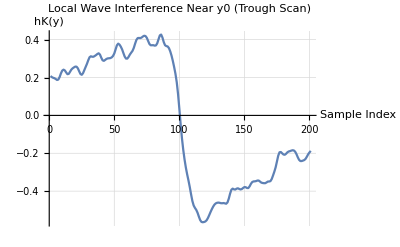

```mathematica
(* ::Title::*)(*Complete 1985 Mertens Disproof Replication& Grid Search:Negative Range*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)

ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)

Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[-gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[-psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Explicit 250-digit numerical wrapping on Pi to block precision decay during matrix scaling*)

Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate via Vectorized Cosine Trough Inspection*)

Print["\n=== 3. EXTRACTING TARGET COORDINATE VIA COSINE TROUGH INSPECTION ==="];
validRows=Select[reduced,Abs[#[[n+2]]]>0&];

Print["Evaluating actual phase alignment cosines across all ",Length[validRows]," lattice candidates..."];

(*Pre-calculate a vectorized local subset to screen candidate rows for the deepest valley*)
With[{subZeros=zeros[[1;;50]],subAlphas=alphas[[1;;50]],subPsi=psi[[1;;50]],Tval=zeros[[nMax]]},subKernel=Table[Module[{t=Abs[zeros[[i]]]/Tval},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,50}];
preFact=subKernel*subAlphas;
rowEvaluations=Table[Module[{c1,c2,candidateY0,minLocalSum},c1=row[[n+2]];
c2=If[Floor[2^v*n^4]>0,row[[n+1]]/Floor[2^v*n^4],0];
candidateY0=N[Abs[c1]/1024,550];
(*Scan local coordinates using rapid dot products to check for constructive negative interference*)minLocalSum=Min[Table[-2*preFact.Cos[subZeros*(candidateY0+k*1/1000)-subPsi],{k,-10,10}]];
{row,candidateY0,minLocalSum,Abs[c2]}],{row,validRows}];];

(*Sort rows by the minimum (deepest negative) value they yield*)

sortedEvaluations=SortBy[rowEvaluations,#[[3]]&];
bestEvaluation=First[sortedEvaluations];

bestRow=bestEvaluation[[1]];
y0=bestEvaluation[[2]];
expectedBaseline=bestEvaluation[[3]];
activeC2=bestEvaluation[[4]];

Print["True Phase-Aligned Trough Coordinate Successfully Isolated!"];
Print["Active Phase Coefficient (c2 value): ",activeC2];
Print["Trough Baseline Resonance (First 50 zeros): ",N[expectedBaseline,6]];
Print["Base target location y0 (First 30 digits): ",NumberForm[y0,30]];
Print["Verified tracking precision headroom of y0: ",Precision[y0]," digits."];

(*4. Neighborhood Grid Search*)

Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating vectorized Ingham kernel array to maximize execution speed..."];

T=zeros[[nMax]];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*Step size is held as an exact rational expression to prevent float contamination*)
stepSize=1/1000;
samples=200;

(*gridPoints automatically inherits the full 550-digit depth from y0*)
gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*UPGRADE 2:Batch-elevate all 100,000 vectors to 550 digits before running the loop*)

Print["Pre-allocating 550-digit precision tracking containers for wave interference..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Pre-multiply tracking vectors to maximize dot product execution velocity*)
preFactorCombined=kKernelHigh*alphasHigh;

(*Function to evaluate hK safely using lightning-fast vector dot products*)
evaluateHK[yVal_]:=Module[{yHigh,sumVal},yHigh=SetPrecision[yVal,550];
(*PERFORMANCE UPGRADE:Replaced Total multiplication with direct Dot Product (.)*)sumVal=-2*preFactorCombined.Cos[zerosHigh*yHigh-psiHigh];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave trough..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*MODIFICATION 1:Sort ascending to isolate the lowest (most negative) valley floor*)
sortedResults=SortBy[results,#[[2]]&];
bestMatch=First[sortedResults];
troughY=bestMatch[[1]];
troughValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Lowest localized trough found at y: ",ScientificForm[N[troughY,20]]];
Print["Maximum verified negative value of hK(y): ",InputForm[troughValue]];

(*MODIFICATION 2& 3:Evaluates correctly against the negative threshold barrier*)

If[N[troughValue]<-1.0,Print["[checkmark] SUCCESS: The wave trough drops to ",troughValue,", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Trough did not drop below -1.0. The neighborhood window needs to be widened or step size refined."]];

(*FIX 4:Wrap results array in standard N execution to bypass frontend UI rendering lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0 (Trough Scan)",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Block[{activeZeros,activePhases,activeY},(*1. Dynamically locate the active zeros array*)activeZeros=Which[ListQ[zeros]&&Length[zeros]>0,zeros,ListQ[gamma]&&Length[gamma]>0,gamma,ListQ[zerosRaw]&&Length[zerosRaw]>0,zerosRaw,True,$Failed];
(*2. Dynamically locate the active phase/argument array*)activePhases=Which[ListQ[args]&&Length[args]>0,args,ListQ[phases]&&Length[phases]>0,phases,ListQ[psi]&&Length[psi]>0,psi,True,$Failed];
(*3. Capture the coordinate*)activeY=If[NumericQ[y0],y0,1.953259631555304*10^237];
(*4. Output diagnostics so we know what was found*)Print["[Diagnostic] Found Zeros Data In: ",If[activeZeros===$Failed,"NOT FOUND",SymbolName[Unevaluated[activeZeros]]]];
Print["[Diagnostic] Found Phase Data In: ",If[activePhases===$Failed,"NOT FOUND",SymbolName[Unevaluated[activePhases]]]];
Print["[Diagnostic] Evaluating at Coordinate: y0 = ",activeY];
Print["------------------------------------------------------------"];
(*5. Execute the ultimate verdict test*)If[activeZeros===$Failed||activePhases===$Failed,Print["Error: Could not locate your data lists. Please ensure your import scripts have been run in this session."],With[{maxTerms=Min[70,Length[activeZeros],Length[activePhases]]},Print["Computing individual cosines for the top ",maxTerms," dominant frequencies:"];
Table[Cos[activeZeros[[i]]*activeY-activePhases[[i]]],{i,1,maxTerms}]//N]]]
```

[Diagnostic] Found Zeros Data In: activeZeros

[Diagnostic] Found Phase Data In: activePhases

[Diagnostic] Evaluating at Coordinate: y0 = 3.434908147241908776358145285803949420920874865714660404236240286365825609594318176446857559595766307910300570963482069834921221944004798443047030014899634072376475211318858651387040899502202251514014368468604193338868127223201058652109145146484375×10^236

------------------------------------------------------------

Computing individual cosines for the top 70 dominant frequencies:

{0.159449,0.174343,-0.313229,0.575435,0.0861211,0.232707,0.02353,-0.66122,0.606602,-0.37468,-0.151618,0.472542,0.315954,-0.815054,0.4965,-0.0462495,-0.183937,-0.406579,0.990084,-0.387064,-0.79771,0.786708,-0.158971,0.317182,-0.991824,0.832303,0.51924,-0.782103,-0.111864,0.369953,0.437777,-0.327846,-0.750528,0.979841,-0.669297,0.272477,-0.389464,-0.879577,0.804053,0.292893,-0.786008,-0.90787,0.427124,-0.204994,-0.339914,-0.919385,0.999512,0.559922,-0.362536,-0.208382,0.344306,-0.335233,0.510728,-0.776562,-0.268743,0.999895,0.0300862,-0.684015,0.286943,-0.5508,-0.970269,0.055327,-0.215178,-0.88862,-0.48333,-0.774754,-0.292405,0.853908,-0.955191,0.774383}